```mathematica
ChangeSymbol[s_]:=Symbol[StringReplace[SymbolName[s],"v"->"n"]]
```

```mathematica
SetDifference[full_,small_]:=Select[full,!MemberQ[small,#]&]
```

```mathematica
Map[ChangeSymbol[#]&,allGraphs5[351,"colofour"]]
```

n12x345+n12x34x5+n12x35x4+n12x3x45+n12x3x4x5+n1345x2+n134x2x5+n135x2x4+n13x2x45+n13x2x4x5+n145x2x3+n14x2x35+n14x2x3x5+n15x2x34+n15x2x3x4+n1x2x345+n1x2x34x5+n1x2x35x4+n1x2x3x45+n1x2x3x4x5

```mathematica
Descendents[g_,vertices_]:=Block[{result={},nodes,edges,current},
nodes=vertices;
While[nodes≠{},
current=First[nodes];
nodes=Rest[nodes];
edges=Select[EdgeList[g],#[[1]]==current&];
result=Join[result,edges];
nodes=Join[nodes,Map[#[[2]]&,edges]];
];
result
]
```

```mathematica
MobiusGraphDouble[key_,key2_,allGraphs_]:=Block[{
form=allGraphs[key,"colofourrealnull"],
form2=allGraphs[key2, "colofourrealnull"],
form3=Map[ChangeSymbol[#]&,allGraphs5[key2,"colofour"]],pairs, vars, blocks=Association[],c,edges,edges2,set, found=Association[],mob,realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],nonRoot,edgesTrans},
vars=ListofVars[form];
Table[blocks[k]={},{k,0,5}];
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}];
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],
AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,5}];
pairs=Subsets[ListofVars[form3],{2}];
edges2={};
Table[With[{e=DirectedEdge[
p[[2]],
p [[1]]]},
If[MemberQ[edges,e],edges2=Append[edges2,e]]],{p,pairs}
];
mob=MobiusGraph4[key2,allGraphs];
nonRoot=Select[VertexList[mob],VertexInDegree[mob,#]>0&];
edgesTrans=Descendents[Graph[vars,edges],nonRoot];
Graph[vars,edges,VertexLabels->Table[n->Placed[Tooltip[Rotate[
TableForm[{Style[n,10,"Calibri",If[Coefficient[form3,n]==0,Black,Blue]],Style[Coefficient[form2,n],Bold,If[Coefficient[form2,n]==0,Blue,Red]]},TableAlignments->Center],
Pi/6],found[n,"graph"]],{Left}
],{n,vars}],GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Top},
EdgeStyle->Join[
Map[#->{Thick,Darker[Green]}&,Select[edgesTrans,!MemberQ[edges2,#]&&!MemberQ[EdgeList[mob],#]&]],
Map[#->{Thick,Blue}&,edges2]
],
GraphHighlight->Join[VertexList[mob],EdgeList[mob]],
GraphHighlightStyle->"Thick",
ImageSize->820]
]
```

```mathematica
repBase5=Table[allGraphs5[k,"colofour"]->Labeled[Graph[allGraphs5[k,"graph"]],Style[allGraphs5[k,"colofour"],Blue,12],ImageSize->{50,50}],{k,allGraphs5AtomKeys}];
```

```mathematica
SummaryPrint5[k_]:=With[
{g=MobiusGraphDouble[K5Key,k,allGraphs5], gr=allGraphs5[k,"graph"]},
Framed[
Labeled[
Row[{
Labeled[Graph[gr,ImageSize->{40,40}],Style[k,Bold,12, Underlined,Red]],
Rotate[g,Pi/2]
}],
{Style[StandardForm[allGraphs5[k,"colofourrealnull"]],Darker[Green],12],
Column[
{Style[TraditionalForm[ ChromaticPolynomial[gr,x]],Blue],Style[TraditionalForm[ ChromaticPolynomial[gr,x]//Factor],Red],Style[ChromaticPolynomial[gr,3],Blue],
Framed[Style[StandardForm[((allGraphs5[k,"colofour"])/.repBase5)],Darker[Green],12]]},
Center
]
},
{Top,Bottom,Bottom}
]
]
]
```

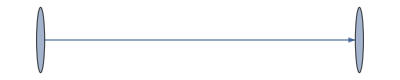

```mathematica
Graph[{1->2},GraphLayout->{"LayeredDigraphEmbedding","Orientation"->Left}]
```

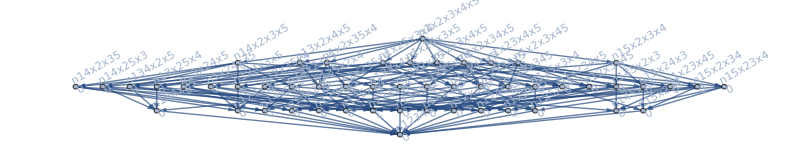
{-Graphics-26979-Graphics-n1235x4-n12x35x4-n135x2x4+n1x2x35x4x^4-2 x^3+x^2
(x-1)^2 x^2
36
-Graphics-v1x2345+-Graphics-v14x235+-Graphics-v1x235x4+-Graphics-v1x2x345+-Graphics-v14x2x35+-Graphics-v1x24x35+-Graphics-v1x2x35x4}

```mathematica
Table[
SummaryPrint5[k]
,{k,RandomSample[ Keys[allGraphs5],1]}
]
```